```mathematica
data=Import["C:\\Users\\HILL\\MEGASync\\msc\\measurements\\2020-02-03\\RefCurve_115654.txt.Wfm.csv","Table","FieldSeparators"->";"];
```

```mathematica
t=Subdivide[3.8*^-7,1.62*^-6,2000-1];
ch1=data[[All,1]];
ch2=data[[All,2]];
ch3=data[[All,3]];
```

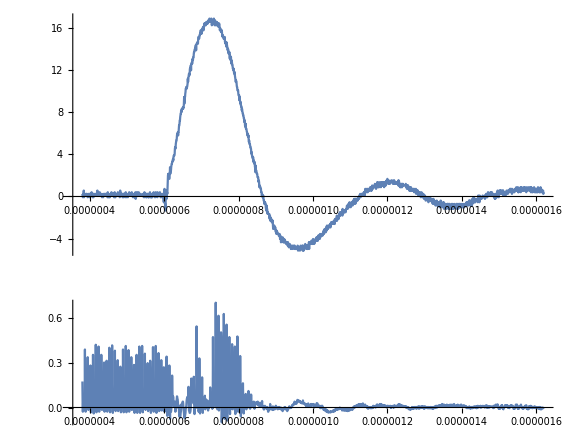

```mathematica
GraphicsColumn[{
ListLinePlot[Thread[{t,ch2}],PlotRange->All,AspectRatio->1/2,AxesStyle->{#,#}&@@{{Black,Thick}}]
,
ListLinePlot[Thread[{t,ch3}],PlotRange->All,AspectRatio->1/4]
},
GridLines->{Table[200+4i,{i,4}],None},GridLinesStyle->{{Black,Dashed,Red},None}
,ImageSize->Large
]
```